# Agujeros negros regulares

```mathematica
detg:=Assuming[NN[r]>0&&r>0&&Sin[θ]^4>0&&Sin[ϕ]>0,Simplify[Sqrt[-Det[g]]]]
```

## Densidades lagrangianas GQTG

```mathematica
Z[1]:=6/r^2-(6 f[r])/r^2-(6 f'[r])/r-(6 f[r] NN'[r])/(r NN[r])-(3 f'[r] NN'[r])/NN[r]-f''[r]-(2 f[r] NN''[r])/NN[r]
Z[2]:=1/(r^3 NN[r])12 (-3 r f'[r] NN'[r]+NN[r] (2 (-1+f[r]) f'[r]+r f'[r]^2+r (-1+f[r]) f''[r])+f[r] ((-2+5 r f'[r]) NN'[r]-2 r NN''[r])+2 f[r]^2 (NN'[r]+r NN''[r]))
Z[3]:=-1/(r^6 NN[r])(-1+f[r]) (NN[r] (2+2 f[r]^2+6 r f'[r]+6 r^2 f'[r]^2-3 r^2 f''[r]+f[r] (-4-6 r f'[r]+3 r^2 f''[r]))+3 r (-3 r f'[r] NN'[r]+f[r] ((2+7 r f'[r]) NN'[r]-2 r NN''[r])-2 f[r]^2 (NN'[r]-r NN''[r])))
```

## Lagrangiano

```mathematica
L:=Collect[Simplify[(Z[1]/3+(α/6)*Z[2]-α^2*Z[3])*detg/(Sin[ϕ]*Sin[θ]^2)],{NN[r],NN'[r],NN''[r]}]
```

Verificación condición GQTG

```mathematica
L1f=Simplify[L/.NN[r]->1/.NN'[r]->0/.NN''[r]->0]
```

-1/3 r (-6+6 f[r]+6 r f'[r]+r^2 f''[r])+2 α (2 (-1+f[r]) f'[r]+r f'[r]^2+r (-1+f[r]) f''[r])+1/r^3 α^2 (-1+f[r]) (2+2 f[r]^2+6 r f'[r]+6 r^2 f'[r]^2-3 r^2 f''[r]+f[r] (-4-6 r f'[r]+3 r^2 f''[r]))

```mathematica
Simplify[D[L1f,f[r]]-D[D[L1f,f'[r]],r]+D[D[L1f,f''[r]],{r,2}]]
```

0

## Solución

```mathematica
F0'[r_]:=Coefficient[L,NN[r]]
F1[r_]:=Coefficient[L,NN'[r]]
F2[r_]:=Coefficient[L,NN''[r]]
funcion1=Simplify[Integrate[F0'[r],r]-F1[r]+D[F2[r],r]]
```

(r^4+α^2-(r^4+2 r^2 α+3 α^2) f[r]+α (r^2+3 α) f[r]^2-α^2 f[r]^3)/r^2

```mathematica
sol=f[r]/. Solve[funcion1==μ,f[r],Reals][[1]]
```

Root[-r^4-α^2+r^2 μ+(r^4+2 r^2 α+3 α^2) #1+(-r^2 α-3 α^2) #1^2+α^2 #1^3&,1]

```mathematica
ToRadicals[sol]
```

-(-r^2 α-3 α^2)/(3 α^2)-(2 2^(1/3) r^4)/(3 (-7 r^6 α^3-27 r^2 α^5-27 r^2 α^4 μ+√(32 r^12 α^6+(-7 r^6 α^3-27 r^2 α^5-27 r^2 α^4 μ)^2))^(1/3))+((-7 r^6 α^3-27 r^2 α^5-27 r^2 α^4 μ+√(32 r^12 α^6+(-7 r^6 α^3-27 r^2 α^5-27 r^2 α^4 μ)^2))^(1/3))/(3 2^(1/3) α^2)

```mathematica
Clear[α,μ]
```

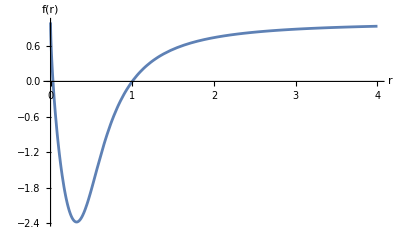

```mathematica
α:=0.03
μ:=1
graphf3=Plot[{sol},{r,0,4},AxesLabel->{"r","f(r)"},PlotRange->All]
```